## Point Drawings

Just points -- ~1000 and then ~15000.

```mathematica
pointsList = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\mesh_points_cgal_1000.csv","Data"];
```

```mathematica
ListPointPlot3D[pointsList]
```

-Graphics3D-

```mathematica
manyPointsList = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\mesh_points_cgal_15000.csv","Data"];
```

```mathematica
ListPointPlot3D[manyPointsList]
```

-Graphics3D-

```mathematica
Show[%3,Axes->False]
```

-Graphics3D-

```mathematica
Show[%4,Boxed->False]
```

-Graphics3D-

```mathematica
torusPointsList = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\torus_points_cgal.txt","Data"];
```

```mathematica
ListPointPlot3D[torusPointsList]
```

-Graphics3D-

## Mesh Drawings

~1000-point mesh.

```mathematica
Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\heightmap1000.off"]
```

-Graphics3D-

15000-point mesh.

```mathematica
Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\heightmap15000.off"]
```

-Graphics3D-

```mathematica
Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\heightmap_performance.off"]
heightmapPoints = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\heightmap_performance.off","VertexData"]
ListPointPlot3D[heightmapPoints,Boxed->False]
```

-Graphics3D-

-Graphics3D-

```mathematica
Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\simplified.off"]
simplifiedMeshPoints = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\simplified.off","VertexData"]
```

-Graphics3D-

```mathematica
ListPointPlot3D[simplifiedMeshPoints,Boxed->False]
```

-Graphics3D-

Torus mesh.

```mathematica
Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\torus.off"]
```

-Graphics3D-

## Parade of Tori

```mathematica
rb20mesh = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\torusrb20.off"]
rb15mesh = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\torusrb15.off"]
rb12mesh = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\torusrb12.off"]
rb09mesh = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\torusrb09.off"]
rb08mesh = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\torusrb08.off"]
rb07mesh = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\torusrb07.off"]
rb05mesh = Import["C:\\Users\\Toler\\OneDrive - Emory University\\sussmangroup_research\\code\\cgal_project\\visualize\\meshes\\torusrb05.off"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

## Comparing Approximate Distance (via CGAL) to True Distance

### Varying bounding radius of individual triangles

```mathematica
rbVsError = {{.05,2.00022-2},{.07,1.99944-2},{.08,1.99911-2},{.09,1.99819-2},{.12,1.99696-2},{.15,1.99581-2},{.20,1.99528-2},{.30,1.98470-2},{.50,1.95204-2},{.80,1.97215-2}};
```

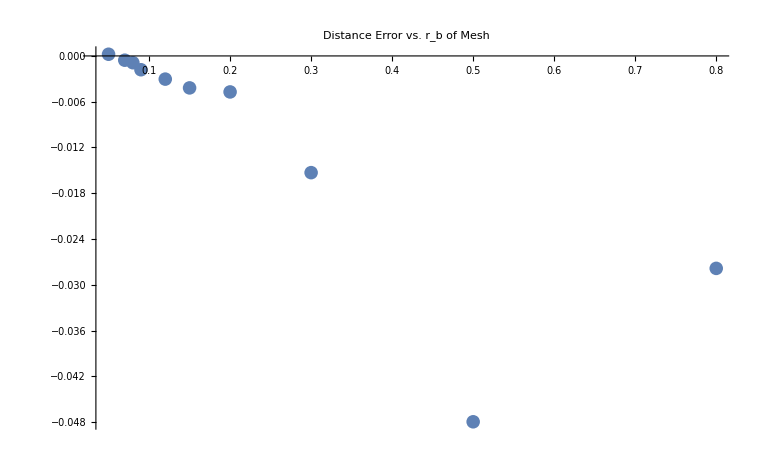

```mathematica
ListPlot[rbVsError,PlotRange->All,PlotLabel->"Distance Error vs. r_b of Mesh"]
```

```mathematica
.05:2.00022
.07:1.99944
.08:1.99911
.09:1.99819
.12:1.99696
.15:1.99581
.20:1.99528
.30:1.98470
.50:1.95204
.80:1.97215
```